```mathematica
pdb=Import[NotebookDirectory[]<>"fmet_coords.xyz","Table"];(*import the molecule PDB*)
Graphics3D[{Thickness[0.01],Line[pdb]}]
```

-Graphics3D-

```mathematica
AuR=1.46;(*gold atom radius*)
NpR=200;(*nano particle radius*)
MoL=60;(*molecule's longest length*)
BoxL=4MoL;(*simulation box size*)
NpSurf=4π NpR^2;(*nano particle suface area*)
Print["Nanoparticle surface bead number: ",AuN=Round[NpSurf/AuR^2/100]](*gold atom number*)
Print["molecule number: ",MoN=Round[NpSurf/MoL^2]](*molecule chain number*)
Print["molecule bead number: ",MoN*221](*total bead number in molecules*)
positive={{0,NpR+4MoL},{0,NpR+4MoL},{0,NpR+4MoL}};(*the range for positive (x,y,z)*)
coord[seed_]:=(c=RandomReal[{-1,1},3])/EuclideanDistance[c,{0,0,0}];(*generate random (x,y,z) coordinates on sphere*)
model[NpR_,AuN_,MoL_,r1_,MoN1_,r2_,MoN2_,region_]:=(
points[r_,n_,c_]:=ListPointPlot3D[Table[r coord[0],{i,n}],PlotStyle->c];(*generate nano particle*)
vectors[r_,l_,n_,c_]:=
Graphics3D[Table[c0=coord[1];c1=coord[2];{c,Arrowheads[{0.02}],Arrow[{r c0,r c0+l c1}]},{i,n}]];(*generate random oriented arrows*)
Magnify@Show[vectors[r2,MoL,MoN2,Blue],vectors[r1,MoL,MoN1,Red],points[NpR,AuN,Yellow],BoxRatios->Automatic,Axes->True,PlotLabel->"Initial State (Å)",PlotRange->region](*function to show conformation*)
)
model[NpR,AuN,MoL,NpR+MoL,MoN,NpR+4MoL,MoN,All](*all*)
model[NpR,AuN,MoL,NpR+MoL,MoN,NpR+4MoL,MoN,positive](*only the positive coordinates*)
```

Nanoparticle surface bead number: 2358

molecule number: 140

molecule bead number: 30940

-Graphics3D-

-Graphics3D-

Box Needed: 23

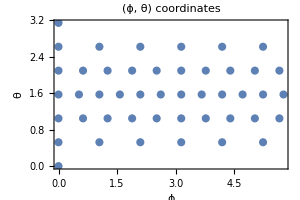
-Graphics-
-Graphics3D-

-Graphics3D-

```mathematica
divide[dθ_]:=((*Divide the sphere surface "uniformly" in term of "solid angle" with points*)
ANGcoords=Append[Prepend[Flatten[Table[Table[{ϕ,θ},{ϕ,0,2π-2π/Round@((2π  Sin[θ])/dθ),2π/Round@((2π  Sin[θ])/dθ)}],{θ,dθ,Pi-dθ,dθ}],1],{0,0}],{0,π}];(*a combination of (ϕ,θ) to divide the sphere. they will be replaced with actual simulation boxes*)
Print["Box Needed: ",BoxN=Length[ANGcoords]/2];(*only need to show the front face*)
XYZcoords=Table[θ=a[[2]];ϕ=a[[1]];(*derive the (x,y,z) coordinates from (r,ϕ,θ)*)
NpR{ Sin[θ]Cos[ϕ], Sin[θ]Sin[ϕ], Cos[θ]},{a,ANGcoords}];
Magnify@Column[{ListPlot[ANGcoords,AspectRatio->Automatic,Frame->True,FrameLabel->{"ϕ","θ"},PlotLabel->"(ϕ, θ) coordinates",ImageSize->300],
Show[Graphics3D[Sphere[{0,0,0},NpR-5]],ListPointPlot3D[Table[XYZcoords[[i]],{i,Length[XYZcoords]}],ColorFunction->"Rainbow",BoxRatios->Automatic,AxesLabel->{"x","y","z"},PlotLabel->"Division Points on Sphere",ImageSize->300]]}])
divide[π/6]
cuboid[BoxL_]:=Flatten[Table[BoxL{x,y,z},{x,-1/2,1/2},{y,-1/2,1/2},{z,0,1}],2];(*a cubic box with box length*)
RawCoord=cuboid[MoL/2];(*use the cuboid as raw coordinates*)
(*RawCoord=pdb;*)(*or use pdb*)
kx={1,0,0};(*unit vector for XYZ axis*)
ky={0,1,0};
kz={0,0,1};
rm[axis_,α_]:=RotationMatrix[α,axis](*the rotation matrix for rotating α angle around axis*)
transform[r_,ϕ_,θ_,RawCoord_]:=Table[rm[kz,ϕ].rm[ky,θ].RawCoord[[i]]+r,{i,Length[RawCoord]}];(*for all raw coordinates, rotate θ around Y, then rotate ϕ around Z. then move along r⃗*)
randomTrans[r_,RawCoord_]:=transform[r,RandomReal[{0,2π}],RandomReal[{0,π}],RawCoord];(*randomly rotate then move*)
Show[Graphics3D[Sphere[{0,0,0},NpR]],Table[Graphics3D[{Hue[Mod[i,7]/7],PointSize[0.02],Line[transform@@Append[Prepend[ANGcoords[[i]],XYZcoords[[i]]],(*randomTrans[0,RawCoord]*)2RawCoord]]}],{i,1,Length[ANGcoords],5(*skip every 5 molecules. for performance purpose*)}],PlotRange->All,BoxRatios->Automatic]
```

```mathematica
cube=DeleteCases[Flatten[Table[If[EuclideanDistance[RawCoord[[i]],RawCoord[[j]]]==30,{RawCoord[[i]],RawCoord[[j]]},{}],{i,8},{j,8}],1],{}];
Show[Graphics3D[Sphere[{0,0,0},NpR]],Table[Graphics3D[Table[{Hue[Mod[i,7]/7],PointSize[0.02],Line[transform@@Append[Prepend[ANGcoords[[i]],XYZcoords[[i]]],(*randomTrans[0,RawCoord]*)2cube[[l]]]]},{l,Length[cube]}]],{i,1,Length[ANGcoords],1(*skip every 5 molecules. for performance purpose*)}],PlotRange->All,BoxRatios->Automatic]
```

-Graphics3D-

```mathematica
(∫_0^(2π) ∫_0^theta r^2 Sin[theta]ⅆthetaⅆphi)/(∫_0^(2π) ∫_0^π r^2 Sin[theta]ⅆthetaⅆphi)(*derive the ratio of (number on secion)/(number on sphere)*)
```

1/2 (1-Cos[theta])

```mathematica
newcoords[r_,n_,l_]:=((*generate random points on part of the nano particle surface with the same density*)
Print["θ Range:",N@((θRange=ArcSin[l/(√2)/r])/π)*180];(*the θ angle when the four bottom vertex of box are on sphere*)
PartN=Round[n(2π r^2(1-Cos[θRange]))/(4π r^2)];(*the points needed to fill the partial sphere (round)*)
{u,v}=RandomReal[{0,1},{2,PartN}];(*an algorithm to generate random coordinates based on spherical angles*)
{ϕ,θ}={2π u,ArcCos[2v-1] θRange/π};
{x,y,z}={r Sin[θ]Cos[ϕ],r Sin[θ]Sin[ϕ],r Cos[θ]};(*derive (x,y,z) coordinates*)
clip=Transpose[{Clip[x,1/2{-l,l},{"out","out"}],Clip[y,{-l/2,l/2},{"out","out"}],z}];
squareCoords=DeleteCases[Table[If[!MemberQ[clip[[c]],"out"],clip[[c]]],{c,Length[clip]}],Null];(*discard the points out of the square from the round partial sphere*)
Print["Partial surface bead number: ",Length[squareCoords]];(*number of nano particle beads on the partial sphere(square) *)
squareCoords
)
Magnify@Show[ListPointPlot3D[newcoords[NpR,AuN,BoxL],PlotStyle->{Darker@Yellow,Large}],
Graphics3D[{{Red,Line[randomTrans[{MoL,-(√3)/3 MoL,NpR+4.5MoL},pdb]]},
{Red,Line[randomTrans[{-MoL,-(√3)/3 MoL,NpR+4.5MoL},pdb]]},
{Red,Line[randomTrans[{0,(2 √3)/3 MoL,NpR+4.5MoL},pdb]]},
{Blue,Line[randomTrans[{MoL,(-√3)/3 MoL,NpR+3MoL},pdb]]},
{Blue,Line[randomTrans[{-MoL,(-√3)/3 MoL,NpR+3MoL},pdb]]},
{Blue,Line[randomTrans[{0,(2 √3)/3 MoL,NpR+3MoL},pdb]]},
{Orange,Line[randomTrans[{MoL,(-√3)/3 MoL,NpR+1.5MoL},pdb]]},
{Orange,Line[randomTrans[{-MoL,(-√3)/3 MoL,NpR+1.5MoL},pdb]]},
{Orange,Line[randomTrans[{0,(2 √3)/3 MoL,NpR+1.5MoL},pdb]]}}],BoxRatios->Automatic,PlotRange->All]
```

θ Range:58.0519

Partial surface bead number: 444

```mathematica
N@((1/NpR-1/(NpR+MoL))/(1/NpR))(*error for potential approximation*)
N@((1/NpR^2-1/(NpR+MoL)^2)/(1/NpR^2))(*error for force approximation*)
```

0.230769

0.408284